#### Assemblages in 1SDI

```mathematica
Array[σ,4,0];
σ[0]=({{1, 0}, {0, 1}});
σ[1]=PauliMatrix[1];
σ[2]=PauliMatrix[2];
σ[3]=PauliMatrix[3];
σ[0,0]={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}};
u={{1},{0}};
d=({{0},{1}});
ψg=Simplify[Cos[θ](KroneckerProduct[u,u,u])+Sin[θ](KroneckerProduct[d,d,d])];
ψgT=Simplify[ConjugateTranspose[ψg],0<θ<π];
ρg=Simplify[v ψg.ψgT + (1-v)/8 σ[0,0]];
Simplify[Tr[ρg]]
MatrixForm[ρg]
```

1

(1/8 (1+3 v+4 v Cos[2 θ]) | 0 | 0 | 0 | 0 | 0 | 0 | v Cos[θ] Sin[θ]
0 | (1-v)/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-v)/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (1-v)/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (1-v)/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (1-v)/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (1-v)/8 | 0
v Cos[θ] Sin[θ] | 0 | 0 | 0 | 0 | 0 | 0 | 1/8-v/8+v Sin[θ]^2)

```mathematica
θ=π/4;
Simplify[Eigenvalues[({{1/8 (1+3 v+4 v Cos[2 θ]), 0, 0, 0, 0, 0, 0, 0}, {0, (1-v)/8, 0, 0, 0, 0, 0, 0}, {0, 0, (1-v)/8, 0, 0, 0, 0, 0}, {0, 0, 0, (1-v)/8, v Cos[θ] Sin[θ], 0, 0, 0}, {0, 0, 0, v Cos[θ] Sin[θ], (1-v)/8, 0, 0, 0}, {0, 0, 0, 0, 0, (1-v)/8, 0, 0}, {0, 0, 0, 0, 0, 0, (1-v)/8, 0}, {0, 0, 0, 0, 0, 0, 0, 1/8-v/8+v Sin[θ]^2}})]]
Clear[θ]
```

{1/8 (1-5 v),(1-v)/8,(1-v)/8,(1-v)/8,(1-v)/8,1/8 (1+3 v),1/8 (1+3 v),1/8 (1+3 v)}

```mathematica
Reduce[1/8 (1-5 v)<0&&0<v<1,v]
```

1/5<v<1

```mathematica
For[l=1,l<4,l++,
For[i=0,i<2,i++,
S[l,i,0,0]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0]]]];
s[l,i,0,0]=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].S[l,i,0,0].KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].S[l,i,0,0].KroneckerProduct[d,σ[0],σ[0]]];
Print[MatrixForm[s[l,i,0,0]]];
θ=π/4;
g[l,i,0,0]=s[l,i,0,0];
Clear[θ];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD[l,i,0,0]=Simplify[Pgs*g[l,i,0,0]+Pgf*s[l,i,0,0]];
]];
Clear[l,i,j,k]
```

(1/8 (1+v+2 v Cos[2 θ]) | 0 | 0 | 1/2 v Cos[θ] Sin[θ]
0 | (1-v)/8 | 0 | 0
0 | 0 | (1-v)/8 | 0
1/2 v Cos[θ] Sin[θ] | 0 | 0 | 1/8 (1+v-2 v Cos[2 θ]))

(1/8 (1+v+2 v Cos[2 θ]) | 0 | 0 | -1/2 v Cos[θ] Sin[θ]
0 | (1-v)/8 | 0 | 0
0 | 0 | (1-v)/8 | 0
-1/2 v Cos[θ] Sin[θ] | 0 | 0 | 1/8 (1+v-2 v Cos[2 θ]))

(1/8 (1+v+2 v Cos[2 θ]) | 0 | 0 | 1/2 ⅈ v Cos[θ] Sin[θ]
0 | (1-v)/8 | 0 | 0
0 | 0 | (1-v)/8 | 0
-1/2 ⅈ v Cos[θ] Sin[θ] | 0 | 0 | 1/8 (1+v-2 v Cos[2 θ]))

(1/8 (1+v+2 v Cos[2 θ]) | 0 | 0 | -1/2 ⅈ v Cos[θ] Sin[θ]
0 | (1-v)/8 | 0 | 0
0 | 0 | (1-v)/8 | 0
1/2 ⅈ v Cos[θ] Sin[θ] | 0 | 0 | 1/8 (1+v-2 v Cos[2 θ]))

(1/8 (1+3 v+4 v Cos[2 θ]) | 0 | 0 | 0
0 | (1-v)/8 | 0 | 0
0 | 0 | (1-v)/8 | 0
0 | 0 | 0 | (1-v)/8)

((1-v)/8 | 0 | 0 | 0
0 | (1-v)/8 | 0 | 0
0 | 0 | (1-v)/8 | 0
0 | 0 | 0 | 1/8-v/8+v Sin[θ]^2)

```mathematica
θ=π/4;
Simplify[Eigenvalues[({{1/8 (1+v+2 v Cos[2 θ]), 0, 0, 0}, {0, (1-v)/8, I/2 v Cos[θ] Sin[θ], 0}, {0, -I/2 v Cos[θ] Sin[θ], (1-v)/8, 0}, {0, 0, 0, 1/8 (1+v-2 v Cos[2 θ])}})]]
Clear[θ]
```

{1/8 (1-3 v),(1+v)/8,(1+v)/8,(1+v)/8}

```mathematica
Reduce[1/8 (1-3 v)≤0&&0<v<1,{v,θ}]
```

1/3≤v<1

```mathematica
Reduce[1/8 (1-v-4 v Cos[θ] Sin[θ])≤0&&0<v<1&&0<θ<π/4,{v,θ}]
```

1/3<v<1&&1/2 ArcSin[(1-v)/(2 v)]≤θ<π/4

```mathematica
v=1/2;
Simplify[1/2 ArcSin[(1-v)/(2 v)]]//N
Simplify[v]//N
Clear[v]
```

0.261799

0.5

```mathematica
Assemblage fidelity
```

```mathematica
For[l=1,l<4,l++,
Fg[l]=Sum[√Tr[g[l,i,0,0].gD[l,i,0,0]],{i,0,1,1}]];
```

```mathematica
Simplify[Fg[3]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

#### Assemblage fidelity for finite copy 1SDI previous method

```mathematica
u00=({{1},{0},{0},{0}});
u01=({{0},{1},{0},{0}});
u10=({{0},{0},{1},{0}});
u11=({{0},{0},{0},{1}});
ut00=ConjugateTranspose[u00];
ut01=ConjugateTranspose[u01];
ut10=ConjugateTranspose[u10];
ut11=ConjugateTranspose[u11];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
```

```mathematica
Fg0=Simplify[√Tr[g[1,0,0,0].gD[1,0,0,0]]+√Tr[g[1,1,0,0].gD[1,1,0,0]]]
```

1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))

```mathematica
Fg1=Simplify[√Tr[g[2,0,0,0].gD[2,0,0,0]]+√Tr[g[2,1,0,0].gD[2,1,0,0]]]
```

(√(2+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ])))/(√2)

```mathematica
Fg2=Simplify[√Tr[g[3,0,0,0].gD[3,0,0,0]]+√Tr[g[3,1,0,0].gD[3,1,0,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg1=Simplify[1/(√4)(√((ut00.gD101.u00)+(ut00.gD101.u11)+(ut11.gD101.u00)+(ut11.gD101.u11))+√((ut00.gD111.u00)-(ut00.gD111.u11)-(ut11.gD111.u00)+(ut11.gD111.u11)))]
```

{{1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))}}

```mathematica
Simplify[√Tr[g101.gD101]+√Tr[g111.gD111]]
```

1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))

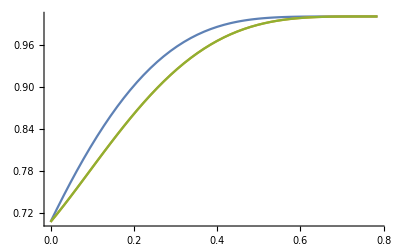

```mathematica
cp=3;
Plot[{1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp)),1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ])),(√(2+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ])))/(√2)},{θ,0,π/4}]
```